# 2x overcomplete basis in 2 dimensions

```mathematica
w = {{1, 0}, {Cos[θ1], Sin[θ1]}, {Cos[θ2], Sin[θ2]}, {Cos[θ2+θ3], Sin[θ2+θ3]}}
```

{{1,0},{Cos[θ1],Sin[θ1]},{Cos[θ2],Sin[θ2]},{Cos[θ2+θ3],Sin[θ2+θ3]}}

```mathematica
MatrixForm[w]
```

(1 | 0
Cos[θ1] | Sin[θ1]
Cos[θ2] | Sin[θ2]
Cos[θ2+θ3] | Sin[θ2+θ3])

## L_2 norm

```mathematica
c2=Function[{θ1,θ2, θ3}, Total[(IdentityMatrix[4]- Dot[w, Transpose[w]])^2, 2]][θ1, θ2, θ3];
dc2=FullSimplify[D[c2, {{θ1, θ2, θ3}}]];
d2c2=FullSimplify[D[c2, {{θ1, θ2, θ3}, 2}]];
```

```mathematica
c2/.{θ1->Pi/2, θ2->0, θ3->Pi/2}
dc2/.{θ1->Pi/2, θ2->0, θ3->Pi/2}
d2c2/.{θ1->Pi/2, θ2->0, θ3->Pi/2}
N[Eigensystem[d2c2/.{θ1->Pi/2, θ2->0, θ3->Pi/2}]]
FullSimplify[dc2/.{θ1->Pi/2, θ3->Pi/2}]
FullSimplify[dc2/.{θ2->0, θ3->-θ1}]
FullSimplify[c2/.{θ2->0, θ3->-θ1}]
```

4

{0,0,0}

{{4,0,4},{0,0,0},{4,0,4}}

{{8.,0.,0.},{{1.,0.,1.},{-1.,0.,1.},{0.,1.,0.}}}

{0,0,0}

{-16 Cos[θ1]^3 Sin[θ1],16 Cos[θ1]^3 Sin[θ1],16 Cos[θ1]^3 Sin[θ1]}

7+4 Cos[2 θ1]+Cos[4 θ1]

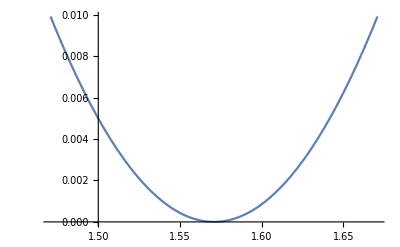

```mathematica
Plot[Cos[x]^2Sin[x], {x, Pi/2-.1, Pi/2+.1}]
```

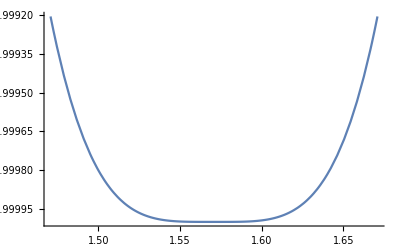

```mathematica
Plot[4 Cos[2 x]+Cos[4 x],{x, Pi/2-.1, Pi/2+.1}]
```

## L_4 norm

```mathematica
c4=Function[{θ1,θ2, θ3}, Total[(IdentityMatrix[4]- Dot[w, Transpose[w]])^4, 2]][θ1, θ2, θ3];
dc4=FullSimplify[D[c4, {{θ1, θ2, θ3}}]];
d2c4=FullSimplify[D[c4, {{θ1, θ2, θ3}, 2}]];
```

```mathematica
c4/.{θ1->Pi/2, θ2->0, θ3->Pi/2}
dc4/.{θ1->Pi/2, θ2->0, θ3->Pi/2}
d2c4/.{θ1->Pi/2, θ2->0, θ3->Pi/2}
N[Eigensystem[d2c4/.{θ1->Pi/2, θ2->0, θ3->Pi/2}]]
FullSimplify[dc4/.{θ2->0, θ3->θ1}]
FullSimplify[c4/.{θ2->0, θ3->θ1}]
```

4

{0,0,0}

{{-8,8,8},{8,-16,-8},{8,-8,-8}}

{{-27.3137,-4.68629,0.},{{-1.,1.41421,1.},{-1.,-1.41421,1.},{1.,0.,1.}}}

{-16 Cos[θ1]^3 Sin[θ1],0,-16 Cos[θ1]^3 Sin[θ1]}

7+4 Cos[2 θ1]+Cos[4 θ1]

```mathematica
w3= {{1, 0}, {Cos[θ1], Sin[θ1]}, {Cos[θ2], Sin[θ2]}}
```

{{1,0},{Cos[θ1],Sin[θ1]},{Cos[θ2],Sin[θ2]}}

```mathematica
c32=Function[{θ1,θ2}, Total[(IdentityMatrix[3]- Dot[w3, Transpose[w3]])^2, 2]][θ1, θ2];
dc32=FullSimplify[D[c32, {{θ1, θ2}}]];
d2c32=FullSimplify[D[c32, {{θ1, θ2}, 2}]];
```

```mathematica
c32/.{θ1->Pi/2, θ2->Pi/4}
dc32/.{θ1->Pi/2, θ2->Pi/4}
d2c32/.{θ1->Pi/2, θ2->Pi/4}
Eigensystem[d2c32/.{θ1->Pi/2, θ2->0}]
FullSimplify[c32/.{θ1->Pi/2}]
```

2

{-2,0}

{{4,0},{0,0}}

{{4 (1+√2),-4 (-1+√2)},{{-1-√2,1},{-1+√2,1}}}

2

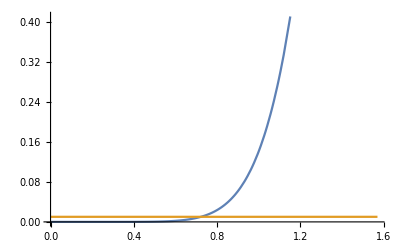

```mathematica
dim=5;
bases=2dim;
saphi[ϕ_, n_]:=2 Pi  Product[Integrate[Sin[θ]^(n-i), {θ,0,ϕ}], {i, 2, n-1}];
saei[n_, m_]:=Pi^(n/2)/Gamma[n/2]/m;
saeic[n_,m_]:=(saphi[Pi/4, n]/saei[n, n])saei[n,m]
Plot[{saphi[ϕ, dim], saeic[dim, bases]}, {ϕ, 0, Pi/2}]
```

```mathematica
NSolve[saphi[ϕ, dim]== saei[dim, bases], ϕ, Reals]
```

NSolve::nsmet: This system cannot be solved with the methods available to NSolve.

NSolve[{π (1-Cos[ϕ]) (ϕ-Cos[ϕ] Sin[ϕ])}==π^2/8,ϕ,Reals]

```mathematica
Table[(180/Pi)FindMinimum[(saphi[ϕ, dim]- saeic[dim, 2 dim])^2, {ϕ, Pi/4}][[2]][[1]][[2]], {dim, 3, 10}]
```

{31.3997,38.8242,41.3929,42.6128,43.2955,43.7185,44.2681,44.4138}

```mathematica
r[[2]][[1]][[2]]
```

1.10833

```mathematica
180*1.1083313806587118/Pi
```

63.5027

```mathematica
ListPlot[{saphi[Pi/4, n], saei[n, n]}, {n, 2, 5}]
```

ListPlot::nonopt: Options expected (instead of {n, 2, 5}) beyond position 1 in ListPlot[{{2\ π\ ∏ i = 2 -1 + n ConditionalExpression[Power[« 2 »]\ Gamma[« 1 »]\ Hypergeometric2F1Regularized[« 4 »], Re[« 1 »] < 1]}, π^n/2/n\ Gamma[n/2]}, {n, 2, 5}]. An option must be a rule or a list of rules.

ListPlot[{{2 π ∏_(i=2)^(-1+n) ConditionalExpression[2^(1/2 (-3+i-n)) Gamma[1/2 (1-i+n)] Hypergeometric2F1Regularized[1/2,1/2 (1-i+n),1/2 (3-i+n),1/2],Re[i-n]<1]},π^(n/2)/(n Gamma[n/2])},{n,2,5}]

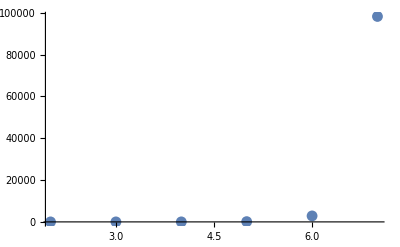

```mathematica
ListPlot[Table[{n, saei[n, n]/saphi[Pi/4, n]}, {n, 2, 7}],PlotRange->All]
```

# 2x overcomplete in 3 dimensions

## L_2 norm

```mathematica
rθrϕ[x_, ϕ_, θ_]:={{Cos[θ], -Sin[θ], 0},{Sin[θ], Cos[θ], 0},{0, 0, 1}}.{{Cos[ϕ], 0, -Sin[ϕ]},{0, 1, 0},{Sin[ϕ], 0, Cos[ϕ]}}.x
```

```mathematica
xhat = {1, 0, 0};
w3 = {xhat,  rθrϕ[xhat, ϕ1, θ1], rθrϕ[xhat, ϕ2, θ2], rθrϕ[xhat, ϕ3, θ3], rθrϕ[rθrϕ[xhat, ϕ4, θ4], ϕ3, θ3], rθrϕ[rθrϕ[xhat, ϕ5, θ5], ϕ3, θ3]};
```

```mathematica
c2= Function[{ϕ1,ϕ2,ϕ3,ϕ4,ϕ5,θ1,θ2,θ3,θ4,θ5},Total[(IdentityMatrix[6]- Dot[w3, Transpose[w3]])^2, 2]][ϕ1,ϕ2, ϕ3,ϕ4, ϕ5,θ1,θ2, θ3,θ4, θ5];
dc2=D[c2, {{ϕ1,ϕ2,ϕ3,ϕ4,ϕ5,θ1,θ2,θ3,θ4,θ5}}];
d2c2=D[c2, {{ϕ1,ϕ2,ϕ3,ϕ4,ϕ5,θ1,θ2,θ3,θ4,θ5}, 2}];
```

```mathematica
FullSimplify[c2/.{ϕ1->0, θ1->Pi/2,ϕ2->Pi/2, θ2->0,ϕ4->0, θ4->Pi/2,ϕ5->Pi/2, θ5->0}]
FullSimplify[dc2/.{ϕ1->0, θ1->Pi/2,ϕ2->Pi/2, θ2->0,ϕ4->0, θ4->Pi/2,ϕ5->Pi/2, θ5->0}]
FullSimplify[d2c2/.{ϕ1->0, θ1->Pi/2,ϕ2->Pi/2, θ2->0,ϕ4->0, θ4->Pi/2,ϕ5->Pi/2, θ5->0}]
es=Eigensystem[d2c2]/.{ϕ1->0, θ1->Pi/2,ϕ2->Pi/2, θ2->0,ϕ4->0, θ4->Pi/2,ϕ5->Pi/2, θ5->0}
```

6

{0,0,0,0,0,0,0,0,0,0}

{{4,0,0,4 Cos[θ3] Cos[ϕ3],-4 Cos[2 ϕ3] Sin[θ3],0,0,0,-4 Cos[θ3] Sin[ϕ3],0},{0,4,0,4 Cos[ϕ3] Sin[θ3],4 Cos[θ3] Cos[2 ϕ3],0,0,0,-4 Sin[θ3] Sin[ϕ3],0},{0,0,0,0,0,0,0,0,0,0},{4 Cos[θ3] Cos[ϕ3],4 Cos[ϕ3] Sin[θ3],0,4,0,4 Cos[2 θ3] Sin[ϕ3],0,0,0,0},{-4 Cos[2 ϕ3] Sin[θ3],4 Cos[θ3] Cos[2 ϕ3],0,0,4,-8 Cos[θ3] Cos[ϕ3] Sin[θ3] Sin[ϕ3],0,0,0,0},{0,0,0,4 Cos[2 θ3] Sin[ϕ3],-8 Cos[θ3] Cos[ϕ3] Sin[θ3] Sin[ϕ3],4,0,0,4 Cos[2 θ3] Cos[ϕ3],0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{-4 Cos[θ3] Sin[ϕ3],-4 Sin[θ3] Sin[ϕ3],0,0,0,4 Cos[2 θ3] Cos[ϕ3],0,0,4,0},{0,0,0,0,0,0,0,0,0,0}}